```mathematica
CityData[All,"Preload"];
RebuildPacletData[];
```

```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

```mathematica
<<IGraphM`;
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
(*https://mathematica.stackexchange.com/questions/18625/avoiding-grid-lines-inside-filled-area-in-regionplot-exported-as-pdf*)
```

```mathematica
data = Import[NotebookDirectory[]<>"../data/trainline/network.csv", "CSV"];
data = Flatten[{#, N[#[[4]]/#[[3]]]}]&/@data;
max = Max[data[[;;, 9]]];
data = Flatten[{#,(#[[9]]/max)^.2}]&/@data;
data = SortBy[data, -QuantityMagnitude[CityData[#[[1]], "Population"], "People"]&];
data // Dataset
```

```mathematica
g = Graph[#1 <->#2 &@@@ data, VertexLabels->None];
geoLocationGraph=GeoPosition[{#5,#6}]<->GeoPosition[{#7,#8}]&@@@data;

ids = {};
getIndex = (name) ↦(If[Dimensions[Position[ids, name]] == {1, 1}, Position[ids, name][[1, 1]], AppendTo[ids, name]; ids // Length]);
wmat = Table[0, {x, 1, VertexCount@g}, {y, 1, VertexCount@g}];
inverseWmat = Table[0, {x, 1, VertexCount@g}, {y, 1, VertexCount@g}];
(wmat[[getIndex[#1], getIndex[#2]]]=#3/#4) &@@@ data;
(inverseWmat[[getIndex[#1], getIndex[#2]]]=#4/#3) &@@@ data;
wg = WeightedAdjacencyGraph[wmat, DirectedEdges->True];
(*g = AdjacencyGraph[Ceiling[Symmetrize[wmat], 1]];*)
```

# ! ! ! ! TODO FIX THE DOWNLOADS!!! SOME CITIES ARE MISSING!!!

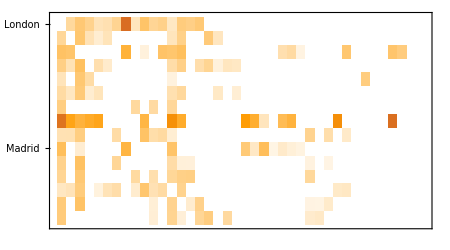

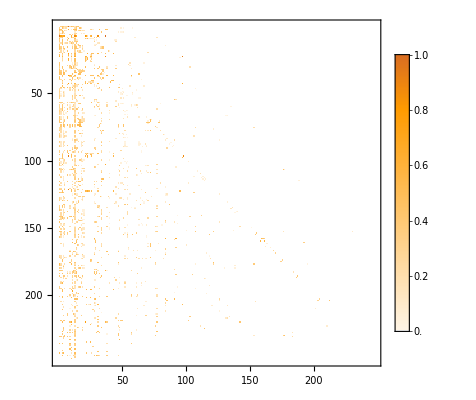

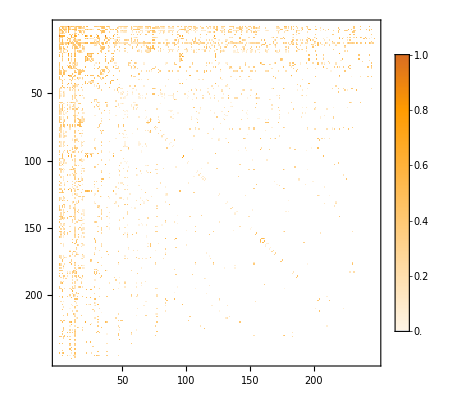

```mathematica
rowticks = Thread[{Range@Length@ids,ids}];
colticks = Thread[{Range@Length@ids,Rotate[#, 90 Degree]&/@ids}];

asymmPlot = MatrixPlot[(Rescale@wmat)[[;;15,;;40]], MaxPlotPoints->Infinity,PlotTheme->{"Scientific", "Web"},ImageSize->{450, 250}, FrameTicks->{rowticks, None, None, colticks}]
asymmFull = MatrixPlot[Rescale@wmat, MaxPlotPoints->Infinity,PlotTheme->{ "Detailed", "Scientific", "Web"}]
symmFull = MatrixPlot[Rescale@Symmetrize[wmat], MaxPlotPoints->Infinity, PlotTheme->{ "Detailed", "Scientific", "Web"}]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/asymmPlotHalf.pdf",asymmPlot]
Export[NotebookDirectory[]<>"../assets/asymmPlotFull.pdf",asymmFull]
Export[NotebookDirectory[]<>"../assets/symmPlotFull.pdf",symmFull]
```

D:\complex-networks\src\../assets/asymmPlotHalf.pdf

D:\complex-networks\src\../assets/asymmPlotFull.pdf

D:\complex-networks\src\../assets/symmPlotFull.pdf

```mathematica
GraphPlot[g] // rasterTrick
(*GraphPlot[wg]; useless *)
GeoGraphPlot[geoLocationGraph, PerformanceGoal->"Speed", RasterSize->1000]
```

-Graphics-

-Graphics-

```mathematica
nodes = VertexList[geoLocationGraph];
degree = VertexDegree[geoLocationGraph];
degreeChart = GeoBubbleChart[{nodes, degree} // Transpose, PerformanceGoal->"Quality", RasterSize->1000, PlotTheme->"Business", GeoBackground->"VectorMonochrome", ImageSize->Large, ColorFunction->"SunsetColors"];
rasterDegreePlot = Rasterize[degreeChart, RasterSize->4000, ImageSize->Medium]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../assets/degreePlot.pdf",rasterDegreePlot]
```

D:\complex-networks\src\../assets/degreePlot.pdf

```mathematica
(*^^ Map is in something projection, the balls are not*)
```

```mathematica
getBezier[x_, y_]:=({GeoPosition@x, GeoPosition[(x+y)/2+Cross[x-y]/8], GeoPosition@y})
getCity = (coords) ↦ GeoNearest["City", coords][[1]] ;
data = Sort[data,#1[[10]]<#2[[10]]&];
i = 0;
ProgressIndicator[Dynamic[i/Length[data]]]
bigPlot = GeoGraphics[
{
(i++;{
Thickness[.002],
 Arrowheads[{{0.01,0.6,{Graphics[{Opacity[1],  Hue[.65,#10, 1],,Polygon[{{-1,1/2},{0,0},{-1,-1/2},{-1,1/2}}]}],0}}}],
 Hue[.65,#10, 1],
Opacity[1],
{Opacity[1],PointSize[.007],Black, Point[VertexList[geoLocationGraph]]},
{Opacity[1],PointSize[.005],Cyan, Point[VertexList[geoLocationGraph]]},
Arrow[
BezierCurve[
getBezier[{#5,#6},{#7,#8}]]
]})&@@@data
},
GeoScaleBar->"Metric", GeoProjection->"Orthographic", GeoGridLines->Automatic, GeoBackground->"VectorMonochrome",  ImageSize->{1414, 1000}
];
rasterBigPlot = Rasterize[bigPlot, RasterSize->4000, ImageSize->Medium]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../assets/rasterBigPlot.pdf",rasterBigPlot]
```

D:\complex-networks\src\../assets/rasterBigPlot.pdf

# Test small world

```mathematica
k = Mean[VertexDegree[g]];
c = GlobalClusteringCoefficient[g];
l = MeanGraphDistance[g];
results = Table[
r = RandomGraph[WattsStrogatzGraphDistribution[g//VertexCount,1, Floor[k]]];
cr = GlobalClusteringCoefficient[r];
lr = MeanGraphDistance[r];
{c/cr //N, l/lr//N}
, {i, 0, 100}] ;
Mean[results]
```

{1.93832,1.27154}

```mathematica
k = Mean[VertexDegree[g]];
c = GlobalClusteringCoefficient[g];
l = MeanGraphDistance[g];
results = Table[
r = RandomGraph[{VertexCount[g], EdgeCount[g]}];
cr = GlobalClusteringCoefficient[r];
lr = MeanGraphDistance[r];
{c/cr //N, l/lr//N}
, {i, 0, 100}] ;
Mean[results]
```

{3.72316,1.04421}

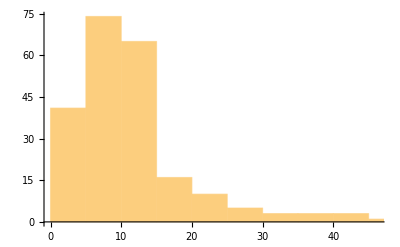

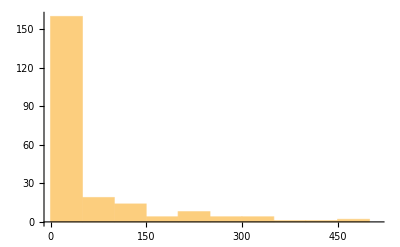

```mathematica
DegreeCentrality[g] // Histogram
BetweennessCentrality[g] // Histogram
```

## Test communities

```mathematica
nodes = VertexList[geoLocationGraph];
degree = BetweennessCentrality[geoLocationGraph];
GeoBubbleChart[{nodes, degree} // Transpose, PerformanceGoal->"Speed", RasterSize->1000, ChartStyle->Orange, GeoBackground->"VectorMonochrome", ImageSize->Large]
```

-Graphics-

```mathematica
CommunityGraphPlot[g, FindGraphCommunities[g, Method->"Centrality"] ,Method->"Hierarchical",VertexLabels->"Name", PlotTheme->{"Large", "Classic"}, PlotLegends->Automatic];
```

```mathematica
communities = FindGraphCommunities[geoLocationGraph,Method->"Centrality"];
subgraphs = Subgraph[geoLocationGraph,#]&/@communities;
colors = Flatten[{{Red, Cyan, Yellow, Green, Pink}, Table[White, {i, 1, Length@communities - 5}]}];
GeoGraphics[
{
{Black, PointSize[.015],Point[#]} &/@ communities,
{#1, PointSize[.012],Point[#2]} &@@@ Transpose[{colors, communities}]
},
GeoScaleBar->"Metric", RasterSize->1000, GeoProjection->"Orthographic", GeoGridLines->Automatic, GeoBackground->"VectorMonochrome", ImageSize->Large
]
```

```mathematica
nodes = VertexList[geoLocationGraph];
degree = IGLocalEfficiency[g];
GeoBubbleChart[{nodes, degree} // Transpose, PerformanceGoal->"Speed", RasterSize->1000, ChartStyle->Pink, GeoBackground->"VectorMonochrome", ImageSize->Large]
```

```mathematica
KirchhoffMatrix[g] // Normal // Eigenvalues // Total ;
(%21 / 229) // N
Det[KirchhoffMatrix[g][[2;;,2;;]]] // N
IGSpanningTreeCount[g] // N
IGGlobalEfficiency[g]

GraphResistanceMatrix[g_?GraphQ]:=Module[{kirchhoffMatrix,pseudoInverse,diagonal},kirchhoffMatrix=KirchhoffMatrix[g];
pseudoInverse=PseudoInverse[kirchhoffMatrix];
diagonal=Diagonal[pseudoInverse];
SparseArray[Outer[Plus,diagonal,diagonal]-pseudoInverse-Transpose[pseudoInverse]]]
Omega = GraphResistanceMatrix[g] (*Can't compute*)
```

# ^^ roba non va NP hard

```mathematica
threshold = 1000000;
i = 0;
ProgressIndicator[Dynamic[i / VertexCount[geoLocationGraph]]]
g1 = VertexDelete[geoLocationGraph, coords_/;(i++; GeoNearest["AdministrativeDivision", coords][[-1]]["Population"] < threshold)];
nodes = VertexList[g1];
degree = DegreeCentrality[g1];
GeoBubbleChart[{nodes, degree} // Transpose, PerformanceGoal->"Speed", RasterSize->1000, PlotTheme->"Business", GeoBackground->"VectorMonochrome", ImageSize->Large]
```

# Check for scale free network (TODO add error for chi square)

{{1.5,0.0445344±0.0134276},{3.,0.0607287±0.0156801},{6.,0.214575±0.0294741},{12.,0.441296±0.0422684},{24.,0.145749±0.0242915},{48.,0.0526316±0.0145974},{96.,0.0364372±0.0121457},{192.,0.00404858±0.00404858}}

{chisqr→{0.,31.3045},p-val→{1,2.65334×10^-6}}

5.21741

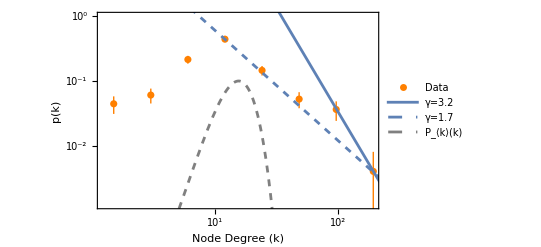

16

```mathematica
vertexDegreeList = VertexDegree@g;
binWidth = PowerRange[1, 600, 2];
hist = Histogram[vertexDegreeList, {binWidth}, "Probability"];
datafromrectangles=Cases[hist,Rectangle[a_,b_,___]:>{Mean[{a[[1]],b[[1]]}],b[[2]] ± Sqrt[b[[2]]] / Sqrt[Length[vertexDegreeList]]},All]
dataNoErrors = Cases[hist,Rectangle[a_,b_,___]:>{Mean[{a[[1]],b[[1]]}],b[[2]]},All];

(*fit  = NonlinearModelFit[datafromrectangles,b x^a,{a, b},x]*)
gamma =3.2;
kmin = 120;
norm = 1/Zeta[gamma];
fit[x_] :=(gamma-1) kmin^(gamma-1)  x^(-gamma)

pearsonTest[obs_List,exp_List]/;Length[obs]==Length[exp]:=Block[{t},t=Total[(obs-exp)^2/exp]//N;
{Rule["chisqr",t],Rule["p-val",SurvivalFunction[ChiSquareDistribution[Length[exp]-1],t]]}]

(*Adjust by hand points on which chi2 is computed*)
testPoints = ((Differences[PowerRange[1, 1200, 2]] / 2) + binWidth)[[;;-3]];
saturationCutoff = 4;
test = pearsonTest[dataNoErrors[[saturationCutoff;;]], Table[{x, fit[x]},{x, testPoints}][[saturationCutoff;;]]]
chisqr = ("chisqr" /. test);
If[chisqr[[1]]!= 0, Print["SOMETHING IS WRONG WITH THE BINS!"]]
chisqrReduced = chisqr[[2]] / (Length[testPoints]-2)

degreePlotLogLog = Show[
ListPlot[datafromrectangles,PlotStyle->Orange,PlotRange->{Full, {0, 1}},PlotTheme->{"Scientific", "FrameGrid"}, ScalingFunctions->{"Log10", "Log10"}, FrameLabel->{"Node Degree (k)", "p(k)"}, LabelStyle->12, PlotLegends->{"Data"}],
Plot[fit[x],{x,-50,1000},PlotRange->Full, ScalingFunctions->{"Log10", "Log10"}, PlotLegends->{"γ=3.2"}],
Plot[30 x^(-1.7),{x,-50,1000},PlotRange->Full, ScalingFunctions->{"Log10", "Log10"}, PlotStyle->{ Dashed}, PlotLegends->{"γ=1.7"}],
Plot[PDF[PoissonDistribution[Mean@vertexDegreeList], x] // Evaluate, {x, 1, 100}, ScalingFunctions->{"Log10", "Log10"}, PlotStyle->{Gray, Dashed}, PlotLegends->{"P_⟨k⟩(k)"}]
(*Graphics[{Black,Rectangle[{3.91,4.42},{4.54,5.98}]}],
Graphics[{White,Rectangle[{3.925,4.5},{4.525,5.9}]}],Graphics[Text[Style["\!\(\*SuperscriptBox[OverscriptBox[\(χ\), \(_\)], \(2\)]\)=1.05",FontSize->16,FontFamily->"Courier"],{4.22,5.2}]]*)
]
Mean[VertexDegree[g]]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/degreePlot.pdf",degreePlot]
Export[NotebookDirectory[]<>"../assets/degreePlotLogLog.pdf",degreePlotLogLog]
```

D:\complex-networks\src\../assets/degreePlot.pdf

D:\complex-networks\src\../assets/degreePlotLogLog.pdf

# Degree correlations

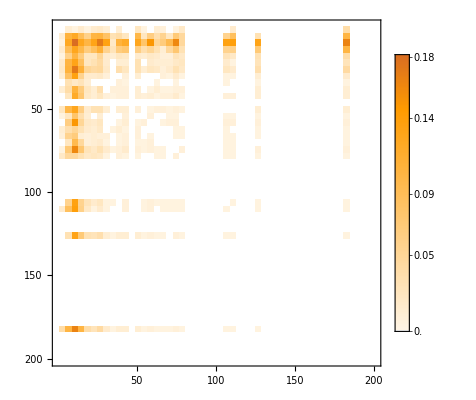

3952

3608

-0.268587

FittedModel[…]

{1.90126,-0.229332}

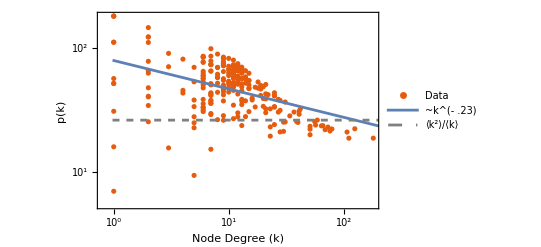

```mathematica
vertexCount = VertexCount@g;
correlationMatrix = Table[Table[0, {y, 0, vertexCount}], {x, 0, vertexCount}];
nodes = Transpose[{VertexList[g], VertexDegree[g]}];
For[i = 1, i <= vertexCount,  i++,
(
currentNode = nodes[[i]];
neighbors = VertexList@NeighborhoodGraph[ g,currentNode[[1]]] ~ DeleteCases ~ currentNode[[1]];
For[j = 1, j<=Length@neighbors, j++,
neighborDegree = VertexDegree[g, neighbors[[j]]];
correlationMatrix[[currentNode[[2]], neighborDegree]]++;
]
)
];
assortativityMatrix = MatrixPlot[Rescale@correlationMatrix , PlotRange->{{0, 200}, {0, 200}},PlotTheme->{ "Detailed", "Scientific", "Web"}, MaxPlotPoints->50]
Total[VertexDegree@g]
Total@Total[correlationMatrix]
GraphAssortativity[g] //N

s = Symmetrize[wmat];
knn[node_] :=  Total[  VertexDegree[g,#]&/@VertexList@NeighborhoodGraph[ g,node]] /  VertexDegree[g, node]
correlationPoints = {VertexDegree[g, #],knn[#]}&/@ VertexList[g];

data2=Log10[correlationPoints];
lm=LinearModelFit[data2,x,x]
estimates=lm["BestFitParameters"]

 assortativityPlot = Show[
ListPlot[correlationPoints , ScalingFunctions->{"Log10", "Log10"}, PlotTheme->{"Scientific", "FrameGrid"},  PlotLegends->{"Data"},FrameLabel->{"Node Degree (k)", "p(k)"}, LabelStyle->12],
Plot[10^(estimates[[1]]+estimates[[2]] Log10[i]), {i, 0, 1000}, ScalingFunctions->{"Log10", "Log10"}, PlotRange->Full, PlotLegends->{"~k^(- .23)"}],
Plot[Variance[VertexDegree@g]/Mean[VertexDegree@g], {x, -100, 1000}, ScalingFunctions->{"Log10", "Log10"}, PlotStyle->{Gray, Dashed}, PlotLegends->{"⟨k^2⟩/⟨k⟩"}]
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/assortativityMatrix.pdf",assortativityMatrix]
Export[NotebookDirectory[]<>"../assets/assortativityPlot.pdf",assortativityPlot]
```

D:\complex-networks\src\../assets/assortativityMatrix.pdf

D:\complex-networks\src\../assets/assortativityPlot.pdf

# Robustness (fake non funziona)

Node connecrivity and edge connectivity are classical robustness measurements

```mathematica
IGVertexConnectivity[g]
IGEdgeConnectivity[g]
```

229

229

## r energy (Tutta questa cosa è una bullshit totale, impossibile riprodurre i risultati)

```mathematica
ComputeREnergy = (wmat) ↦ (
result = {};
wgraph = WeightedAdjacencyGraph[wmat];
dg = DiagonalMatrix[Power[#, -1/2] &/@ VertexDegree[wgraph]];
AppendTo[result, MatrixPlot[dg]];
symmetricWmat = Rescale@(wmat +Transpose@wmat);
ng = N[IdentityMatrix[VertexCount[wgraph]] - (dg . symmetricWmat . dg)];
AppendTo[result, MatrixPlot[ng]];
gamma = Eigenvalues[ng] // Sort;
AppendTo[result, Variance[gamma]];
AppendTo[result, ListPlot[gamma, PlotRange->Full]];
result
);
```

^^ ez  questa  è  la  r  energy  e  deve  stare  tra  0  e  1

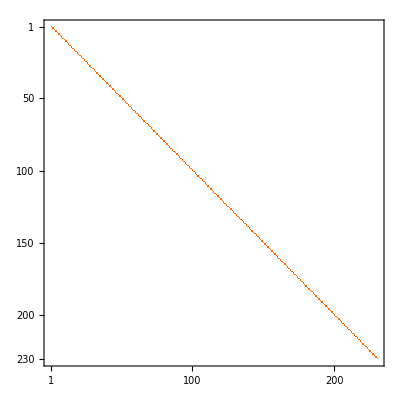
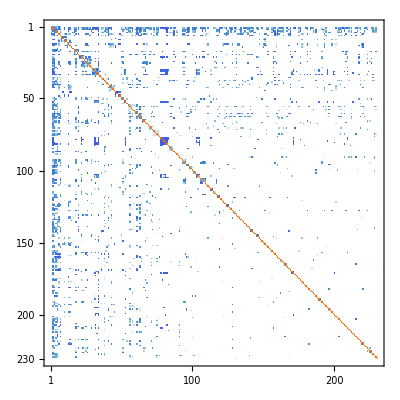
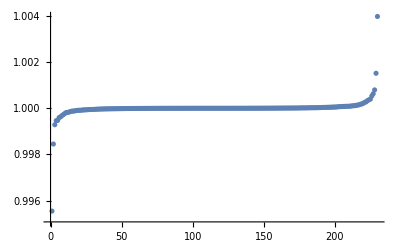
{-Graphics-,-Graphics-,1.93618×10^-7,-Graphics-}

```mathematica
ComputeREnergy[wmat]
```

```mathematica
RandomMatrix = ResourceFunction["RandomMatrix"];
```

```mathematica
wmat2 = RandomMatrix[Real, {0, 10}, 230]
```

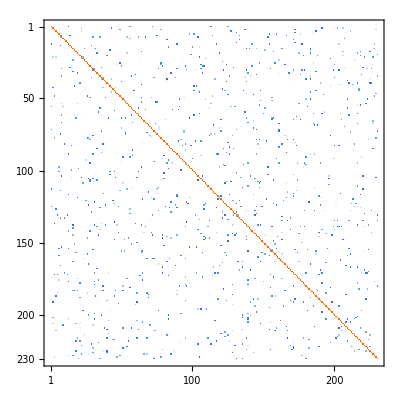
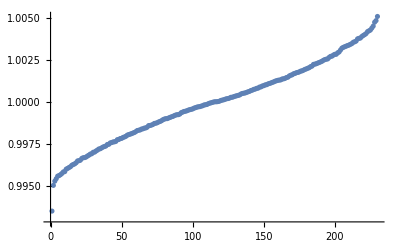
{-Graphics-,-Graphics-,5.76325×10^-6,-Graphics-}

```mathematica
ComputeREnergy[Threshold[wmat2,9.9]]
```

# Actual robustness che funziona

## Random failures

```mathematica
pinf = {};
SetSharedVariable[pinf]
totalNodes = VertexCount[g];
ParallelDo[
runs = {};

For[run = 0, run < 4, run++,
tempGraph = g;
For [i=0, i < nodeRemovedCount, i++,
tempGraph = VertexDelete[tempGraph,RandomChoice[VertexList[tempGraph]]];
];
AppendTo[runs, (Length@Last@Sort@ConnectedComponents@tempGraph)/(totalNodes)];
];

AppendTo[pinf, {nodeRemovedCount, Mean[runs]±StandardDeviation[runs]}];
, {nodeRemovedCount, 0, totalNodes-1}];
```

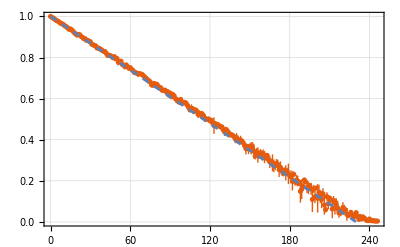

```mathematica
randomFailuresPlot = Show[
ListPlot[pinf, PlotTheme->{"Scientific", "FrameGrid"}],
Plot[-x/230 + 1,{x, 0, 230}, PlotStyle->Dashed]
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/raindomFailuresPlot.pdf",randomFailuresPlot];
```

```mathematica
(*Vertex degree sembra essere buggato per directed network*)
pinf = {};
SetSharedVariable[pinf]
totalNodes = VertexCount[wg];

ParallelDo[

	tempGraph = wg;
	For [i=0, i < nodeRemovedCount, i++,
	tempGraph = VertexDelete[tempGraph,RandomChoice[VertexList[tempGraph]]];
	];
	AppendTo[pinf, {nodeRemovedCount, (Length@Last@Sort@WeaklyConnectedComponents@tempGraph)/(totalNodes)}];

, {nodeRemovedCount, 0, totalNodes}];
ListPlot[pinf]
```

## Molloy reed

(predicts critical threshold for random failures on scale free network)

```mathematica
degrees = VertexDegree[g];
molloyValue = N@Variance[degrees] / Mean [degrees]
breakdownThreshold = 1-1/(molloyValue-1)
N@Variance[degrees]
N@Mean[degrees]
```

21.4216

0.951032

307.912

14.3739

## Targeted attack

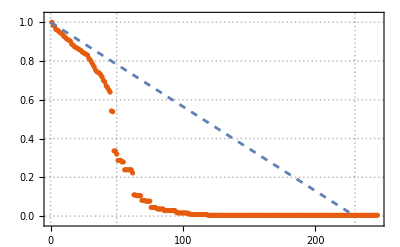

```mathematica
pinfTargeted = {};
totalNodes = VertexCount[g];

tempGraph = g;
Do[
AppendTo[pinfTargeted, (Length@Last@Sort@ConnectedComponents@tempGraph)/(totalNodes)];
maxDegreeNode = Ordering[VertexDegree[tempGraph], -1][[1]];
tempGraph = VertexDelete[tempGraph,VertexList[tempGraph][[maxDegreeNode]]];

, {nodeRemovedCount, 0, totalNodes-1}];
targetedAttackPlot = Show[
ListPlot[pinfTargeted, PlotTheme->{"Scientific", "Detailed"}, FrameTicks->{{0,50,100,150,200,230}, Automatic}, GridLines->{{0, 50, 230}, {0, .2, .4, .6, .8, 1}}, PlotRange->{-.03, 1.03}],
Plot[-x/230 + 1,{x, 0, 230}, PlotStyle->Dashed]
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/targetedAttackPlot.pdf",targetedAttackPlot]
```

D:\complex-networks\src\../assets/targetedAttackPlot.pdf

### (vv critical threshold for attacks on scale free network)

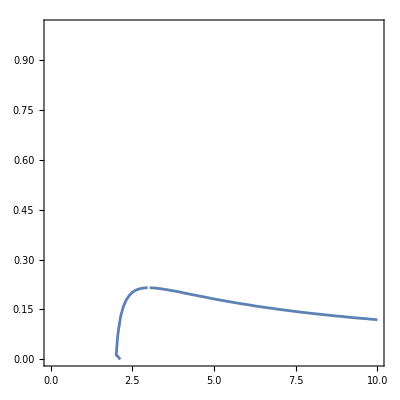

{{fc→236.579},{fc→0.150003}}

```mathematica
kmin = 2;Min[VertexDegree[g]];
bigAssEquation = fc^((2-γ)/(1-γ))==2+((2-γ)/(3-γ)) kmin(fc^((3-γ)/(1-γ))-1);
ContourPlot[bigAssEquation,  {γ, 0, 10}, {fc, 0, 1}]
NSolve[bigAssEquation /. γ->2.2, fc]
```

```mathematica
EdgeCount[g]
```

1653